```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->None]
```

```mathematica
(* get the radius function right *)
```

## Styles and files

```mathematica
runsToGenerate  = {};
```

```mathematica
githubPath= PersistentSymbol["persistentGitHubPath","Local"];
AppendTo[$Path,FileNameJoin[{githubPath,"Packages"}]];
Needs["LatticePhyllotaxis`"];
Needs["DiskStacking`"];
Get["scpPaperStylings.m"]
```

```mathematica
gDrive = PersistentSymbol["persistentGDrive"];
runDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs"}];
eSetDirectory = (* post processed runs, no real reason for this to be different from runDirectory *) FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Esets"}];

draftFigureDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\DraftFigures"}];


getRunByTag[tag_] := Module[{file},
file = FileNameJoin[{runDirectory,StringJoin[tag,".mx"]}];
If[FileExistsQ[file],Return[Import[file]]];
Print["Can't load ", tag, " from ", file];
Abort[]
];
```

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->  jStyle["FontFamily"],FontSize-> n};
paraColours= <|Red-> jParastichyColour[1],Blue-> jParastichyColour[2]|>;
leftRightColours = <|"Left"-> jParastichyColour[1],"Right"-> jParastichyColour[2]|>;
jBaseStyle= jFont[12];

SetAttributes[jExport,HoldFirst];

jExport[fig_] := Module[{figname},
SetDirectory[draftFigureDirectory];
figname=SymbolName[Unevaluated[fig]];
Export[StringJoin[figname,".jpg"],fig,ImageResolution->300];Export[StringJoin[figname,".pdf"],fig,ImageResolution->300];
ResetDirectory[];
fig
];
```

## tlkNonOpposed Illustrative lattice plot

```mathematica
tlkShowParastichyLines[lattice_,lineColourFunction_]  :=  Module[{ll,llines,paraset,plines,numbers,rise,divergence,glines},
ll =Take[Flatten[ LatticePhyllotaxis`latticeLabel[lattice]],2];
llines = Map[LatticePhyllotaxis`latticeParastichyLines[lattice,#]&,ll];
numbers= KeyValueMap[Style[Text[#1,#2],Background->White]&,KeyTake[lattice["namedLatticePoints"],Range[0,10]]];
rise= Translate[Arrow[{{lattice["namedLatticePoints"][1][[1]],lattice["namedLatticePoints"][0][[2]]},lattice["namedLatticePoints"][1]}],{0.05,0}];
divergence= {Arrow[{lattice["namedLatticePoints"][0],{lattice["namedLatticePoints"][1][[1]],lattice["namedLatticePoints"][0][[2]]}}]};
Graphics[{
{jStyle["CylinderColour"],LatticePhyllotaxis`latticeGraphicsCylinder[lattice]}
,{FaceForm[White],LatticePhyllotaxis`latticeCircles[lattice]/. Circle->Disk},
, {Thick,MapIndexed[{lineColourFunction[First[#2]],#1}&,llines]}
,{PointSize[Small],Point[LatticePhyllotaxis`latticePoints[lattice]]}
},PlotRange->{{-1/2,.6},{-0.05,0.4}}
,BaseStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.03]]
]
];

tlkNonOpposed := Module[{lattice,dh},
dh=LatticePhyllotaxis`latticeDivergenceRiseForNonOpposedTC[{2,5}];
lattice = LatticePhyllotaxis`latticeFromDivergenceRise[dh, {-0.1,0.5}];

tlkShowParastichyLines[lattice,jParastichyColour]
];
tlkOpposed := Module[{lattice,dh},
dh=LatticePhyllotaxis`latticeDivergenceRiseForOpposedTC[{2,5}];
lattice = LatticePhyllotaxis`latticeFromDivergenceRise[dh, {-0.1,0.5}];

tlkShowParastichyLines[lattice,jParastichyColour]
];
tlkONotO := GraphicsRow[{tlkOpposed,tlkNonOpposed}]
```

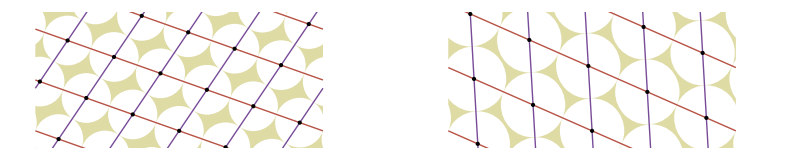

```mathematica
jExport[tlkONotO]
```